# Differentiating Matrix Decompositions

A matrix decomposition splits a matrix A up into a useful product of structured matrices.  For example:

Singular Value Decomposition: A=U.Σ.Vᵀ  where Σ is diagonal with ordered non-negative entries and U and V are orthogonal;

Spectral Decomposition: A=X.Λ.X^-1 where Λ is diagonal;

Symmetric (A=Aᵀ) Spectral Decomposition: A=Q.Λ.Qᵀ  where Λ is diagonal and Q is orthogonal;

Schur Decomposition (A=Aᵀ) Spectral Decomposition: A=Q.T.Qᵀ  where T is pseudo-upper triangular and Q is orthogonal;

Hessenberg Decomposition: A=Q.H.Qᵀ where H is upper Hessenberg and Q is orthogonal. (Direct)

Symmetric (A=Aᵀ) Hessenberg Decomposition: A=Q.T.Qᵀ where T is tridiagonal and Q is orthogonal. (Direct)

These decompositions can be differentiated and some of the results are useful!  By differentiated I mean that you can compute derivatives of the products from the decomposition and the derivative of the data matrix A.  We are going to look at the SVD first. Our second target is the Schur decomposition.

## Differentiating the SVD

The SVD expresses an m×n matrix as the product
	A=U.Σ.Vᵀ
where U and V are orthogonal and Σ is diagonal. For simplicity lets assume the matrix is square and full rank then the product rule gives
	A'=U'.Σ.Vᵀ+U.Σ'.Vᵀ+U.Σ.Vᵀ'
	dA=dU.Σ.Vᵀ+U.dΣ.Vᵀ+U.Σ.dVᵀ
Since  U and V are orthogonal U.Uᵀ=V.Vᵀ=I. Differentiating the first of these gives
	U.(Uᵀ)'+U'.Uᵀ=0
which means that U'.Uᵀ=-(U'.Uᵀ)ᵀ.  In other words, 
	X=U'.Uᵀ 
is a skew matrix. Similarly we have that 
	Y=V'.Vᵀ
is a skew matrix.

Our goal is to compute the diagonal matrix Σ' and the skew matrices X and Y from A' the diagonal matrix Σ and the orthogonal matrices U and V.  Multiply the product rule expression by Uᵀ and V
	Uᵀ.A'.V=Uᵀ.U'.Σ.Vᵀ.V+Uᵀ.U.Σ'.Vᵀ.V+Uᵀ.U.Σ.Vᵀ'.V
orthogonality means this is  
	Uᵀ.A'.V=Uᵀ.U'.Σ+Σ'+Σ.Vᵀ'.V
the definition of X and Y means this is   
	X.Σ+Σ'+Σ.Y=Uᵀ.A'.V
The diagonal entries of X.Σ and Σ.Y are zero so the diagonal of Σ' matches the diagonal of Uᵀ.A'.V.  I am going to write this as
	σ'=diagonal(Uᵀ.A'.V)
Lets check this part of the computation.

```mathematica
m=4; ϵ=0.001;
A=RandomReal[{-1,1},{m,m}]; dA=ϵ RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
dS=Diagonal[Uᵀ.dA.V];
{Diagonal[S],Diagonal[S]+dS,SingularValueList[A+dA]}
(Diagonal[S]+dS)-SingularValueList[A+dA]
```

{{1.81993,1.34058,1.12354,0.335467},{1.82004,1.33999,1.12397,0.334647},{1.82004,1.33999,1.12397,0.334647}}

{-6.28771×10^-7,-2.3686×10^-7,7.75128×10^-8,-1.84774×10^-8}

If we can compute the skew matrices X=U'Uᵀ and Y=V'Vᵀ we will be able to compute the derivatives U' and V'. Our algebraic equation is 
	X.Σ+Σ.Y=B:=Uᵀ.A'.V-Σ'
Note that neither X.Σ or Σ.Y are skew! and the RHS matrix B has zeros on the diagonal. I can transpose to get
	Σᵀ.Xᵀ+Yᵀ.Σᵀ=Bᵀ  or equivalently -Σ.X-Y.Σ=Bᵀ
since X and Y are skew and Σ is diagonal.  Subtracting I get 
	Σ.(X+Y)+(X+Y).Σ=B-Bᵀ
which is a standard diagonal Sylvester/Lyapunov equation. Mathematica, matlab and Julia all have solvers for these linear matrix equations.

Here is what we have so far!

```mathematica
m=4; ϵ=0.01;
A=RandomReal[{-1,1},{m,m}]; dA=ϵ RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
dS=Diagonal[Uᵀ.dA.V];
B=Uᵀ.dA.V-DiagonalMatrix[dS];
Z=XPlusY=LyapunovSolve[S,S,B-Bᵀ];
MatrixForm[XPlusY]
```

(0. | 0.00260848 | 0.00193426 | 0.00615622
-0.00260848 | 0. | -0.00288951 | 0.000272659
-0.00193426 | 0.00288951 | 0. | -0.0044079
-0.00615622 | -0.000272659 | 0.0044079 | 0.)

Of course, Z=X+Y comes out skew and substituting Y=Z-X in
	X.Σ+Σ.Y=B
eliminates Y to give 
	X.Σ-Σ.X=B-Σ.Z 
This is a non standard Sylvester/Lyapunov equation.  The matrices on both sides are constructed or maybe constrained to be skew! For a general non-skew right hand side the equations are inconsistent.  However, we know how to write down the solution as a the Hadamard product
	X=K∘(B-Σ.Z) 
where
	K_(i,j)=(0 | if | i=j
1/(s⟦j⟧-s⟦i⟧) | if | i≠j

```mathematica
K=Table[
If[i==j,0,1/(S⟦j,j⟧-S⟦i,i⟧)],
{i,m},{j,m}];
X=K*(B-S.Z); Y=Z-X;
Map[Norm,{X.S-S.X-(B-S.Z), X.S+S.Y-B}]
```

{2.44631×10^-19,1.75335×10^-18}

The summary is that if I put all of this together I can “differentiate” the SVD.  This is a good time to ask “what can go wrong”.  After that it is time to hide all this stuff in a function.

```mathematica
SVDDiff[A_,dA_,{U_,S_,V_}]:= Module[{ds,B,Z,K,m,n,dX,dY},
{m,n}=Dimensions[A];
ds=Diagonal[Uᵀ.dA.V];
B=Uᵀ.dA.V-DiagonalMatrix[ds];
Z=LyapunovSolve[S,S,B-Bᵀ];
K=Table[If[i==j,0,1/(S⟦j,j⟧-S⟦i,i⟧)],
{i,m},{j,m}];
dX=K*(B-S.Z); dY=Z-dX;
{ds,dX,dY}
]
```

We need to test the function and the construction. I am going to check that I satisfy the starting point
	X.Σ+Σ'+Σ.Y=Uᵀ.A'.V
of the computation.

```mathematica
m=23; ϵ=1.0 10^-6; Id=IdentityMatrix[m];
A=RandomReal[{-1,1},{m,m}]; dA=ϵ RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{ds,dX,dY}=SVDDiff[A,dA,{U,S,V}];
Norm[dX.S+DiagonalMatrix[ds]+S.dY -Uᵀ.dA.V]
```

1.94794×10^-21

This is not actually a check that we are computing the derivative correctly it is a check that we are implementing the plan correctly.  How should we check if the plan is right?  Well one way is to go backwards to the “product rule” from
	X.Σ+Σ'+Σ.Y=Uᵀ.A'.V
So
	U.X.Σ+U.Σ'+U.Σ.Y=A'.V
and 
	U.X.Σ.Vᵀ+U.Σ'.Vᵀ+U.Σ.Y.Vᵀ=A'
which we can check.

```mathematica
m=4; ϵ=1.0 10^-6; Id=IdentityMatrix[m];
A=RandomReal[{-1,1},{m,m}]; dA=ϵ RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{ds,dX,dY}=SVDDiff[A,dA,{U,S,V}];
Norm[U.dX.S.Vᵀ+U.DiagonalMatrix[ds].Vᵀ+U.S.dY.Vᵀ -dA]
```

7.63487×10^-22

```mathematica
MatrixForm[RandomInteger[{-9,9},{3,4}]]
```

(6 | 6 | -2 | -4
-7 | -2 | -6 | 9
-3 | -8 | 1 | 5)

We can rearrange this a bit. I changed some names and stuff.   
	U.dX.S.Vᵀ+U.(S+dS).Vᵀ+U.S.(V.dYᵀ)ᵀ=A+dA
Remember there are missing product terms e.g. dX times dY and/or dS

Differentiate f(x)=x^2 from first principles
	(x+h)^2=x^2+ 2 x h + h^2  looks like  x^2+ 2 x h =f(x)+2x h

### Tuesday the 10th Algebraic Approach

The first principle derivation of the product rule expression is pretty direct
	A=U.S.Vᵀ
Set up the derivative expansion
	A+h dA+…=(U+h dU+…).(S+h dS+…).(V+h dV+…)ᵀ=U.S.Vᵀ+h (dU.S.Vᵀ+U.dS.Vᵀ+U.D.dVᵀ)+…

The first principle derivation of the product rule expression is pretty direct
	A=U.S.Vᵀ
You might like this better without the …
	A+h dA+O(h^2)=(U+h dU+O(h^2)).(S+h dS+O(h^2)).(V+h dV+O(h^2))ᵀ=U.S.Vᵀ+h (dU.S.Vᵀ+U.dS.Vᵀ+U.D.dVᵀ)+O(h^2)

Matching up the terms in the expansion give us the “derivative” starting point 
	dA=dU.S.Vᵀ+U.dS.Vᵀ+U.D.dVᵀ
which we implemented in the function we made last Thursday.  The function returns 
	{ds, dX, dY}
where ds is the diagonal entries of dS and dX=dU Uᵀ and dY=dV.Vᵀ

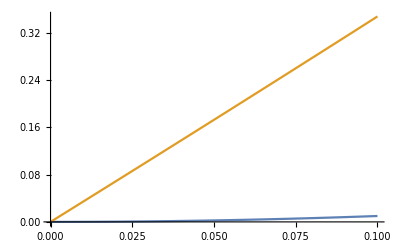

```mathematica
m=4;
{A,dA}=RandomReal[{-1,1},{2,m,m}]; 
{U,S,V}=SingularValueDecomposition[A];
{ds,dX,dY}=SVDDiff[A,dA,{U,S,V}];
dS=DiagonalMatrix[ds];
{dU,dV}={dX.U,dY.V};
Clear[err]
err[h_]:= A+h dA -(U+ h dU).(S+h dS).(V+h dV)ᵀ
Plot[{h^2,Norm[err[h]]},{h,0, 0.1}]
```

## Differentiating a Schur Decomposition

The target is to modify the SVD “differentiation” argument to the Schur Decomposition. 
	A=Q.T.Qᵀ or equivalently T=Qᵀ.A.Q
where Q is orthogonal (Q.Qᵀ=I) and T is upper triangular. Differentiating gives
	A'=Q'.T.Qᵀ+Q.T'.Qᵀ+Q.T.(Qᵀ)' 
and 
	Q'.Qᵀ+Q.(Qᵀ)'=0

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}];
{Q,T}=SchurDecomposition[A];
Map[Norm,{A-Q.T.Qᵀ,Q.Qᵀ}]
```

{3.97528×10^-15,1.}